```mathematica
<<CrossSectionsIceCube`
```

```mathematica
(*physical constants*)
NA=6.02214*10^23; (*avogadros constant*)
ρ=0.92; (*density of ice*)
c=3*10^8;
τμ=2.2*10^-6;
mμ=0.105;
nH20=ρ*NA/18;
nO=nH20;
nH=2*nH20;
GeVtoCM=3.9057007608305083*10^-28;

(* energy loss for muons in ice*)
α=0.00260*ρ*100;
β=0.00000349*ρ*100;
energy[x_, E0_]:=(E0 + α/β)*Exp[-β*x] - α/β +mμ; (*E(x) in ice*)
v[x_,E0_]:=Sqrt[1-(mμ/(energy[x,E0]))^2]*c (*speed of a muon at some energy*)
τNoConst[x_,E0_]:=-mμ/(v[x,E0]*α)*(Log[Abs[Exp[-β*x]*(E0*β+α)-α]]+β*x)(*muon proper time at x plus some const*)
τ[x_,E0_]:=τNoConst[x,E0]-τNoConst[0,E0] (*muon proper time with initial condition*)
(*muon decay including energy loss. x is distance traveled in detector *)
Nμ[x_,E0_]:=N0*Exp[-τ[x,E0]/τμ] (* lorentz boost is energy dependent *)
NμFree[x_,E0_]:=N0*Exp[-x/(c*E0/mμ*τμ)] (*without energy loss*)
MuonLength[E0_]:=1/β*Log[(E0+α/β)/(α/β)] (*length travelled until 0 energy*)

(* muon flux and IceCube parameters*)
N0=7.6*10^11; (*number of muons in 10 years (2400 Hz) *)
lmin:=30; (*minimum detectable LLP decay length in lab*)
L=1000; (*length of IceCube detector*)
lmax[L_,x_]:=L-x-lmin; (*maximum detectable LLP length*)
decayFactor[energy_,max_,min_,m_,ϵ_]:=Module[{lifetime,return,decaylength},
decaylength=c*τDLS[m,ϵ]*energy/m;
If[decaylength<5,return=0,return=Exp[-min/decaylength] - Exp[-max/decaylength]]
If[max<=min,return=0,return=return]
return
]

ΔL=10; (* step length in segmented thin target approximation *)
lengthList=Range[0,L,ΔL];
(* only production *)NLLP[E0_,m_,ϵ_]:=GeVtoCM*Sum[ΔL*Nμ[x,E0]*(nO*σIWWy[energy[x,E0],m,ϵ]+nH*σIWWy[energy[x,E0],m,ϵ]),{x,lengthList}];
(* production and decay -> total detactable events *)
Ndetectable[E0_,m_,ϵ_]:=GeVtoCM*Sum[decayFactor[energy[x,E0],lmax[L,x],lmin,m,ϵ]*ΔL*Nμ[x,E0]*(nO*σIWWy[energy[x,E0],m,ϵ]+nH*σIWWy[energy[x,E0],m,ϵ]),{x,lengthList}];
```

```mathematica
E0=600; (* initial energy of muon *)

(* grid parameters *)
steps=35;
masseslog=Range[Log10[0.1058],Log10[0.145],(Log10[0.145]-Log10[0.1058])/steps];
masses=10^masseslog
epsilonslog=Range[-6,-3.2,0.05];
epsilons=10^epsilonslog
Tuples[{epsilons,masses}];
```

{0.1058,0.106757,0.107723,0.108697,0.10968,0.110673,0.111674,0.112684,0.113703,0.114732,0.11577,0.116817,0.117874,0.11894,0.120016,0.121102,0.122197,0.123302,0.124418,0.125543,0.126679,0.127825,0.128981,0.130148,0.131325,0.132513,0.133712,0.134921,0.136142,0.137373,0.138616,0.13987,0.141135,0.142412,0.1437,0.145}

{1.×10^-6,1.12202×10^-6,1.25893×10^-6,1.41254×10^-6,1.58489×10^-6,1.77828×10^-6,1.99526×10^-6,2.23872×10^-6,2.51189×10^-6,2.81838×10^-6,3.16228×10^-6,3.54813×10^-6,3.98107×10^-6,4.46684×10^-6,5.01187×10^-6,5.62341×10^-6,6.30957×10^-6,7.07946×10^-6,7.94328×10^-6,8.91251×10^-6,0.00001,0.0000112202,0.0000125893,0.0000141254,0.0000158489,0.0000177828,0.0000199526,0.0000223872,0.0000251189,0.0000281838,0.0000316228,0.0000354813,0.0000398107,0.0000446684,0.0000501187,0.0000562341,0.0000630957,0.0000707946,0.0000794328,0.0000891251,0.0001,0.000112202,0.000125893,0.000141254,0.000158489,0.000177828,0.000199526,0.000223872,0.000251189,0.000281838,0.000316228,0.000354813,0.000398107,0.000446684,0.000501187,0.000562341,0.000630957}

```mathematica
(* only production, no decay factor *)
production=Flatten[Table[{m,ϵ,NLLP[E0,m,ϵ]},{m,masses},{ϵ,epsilons}],1];
```

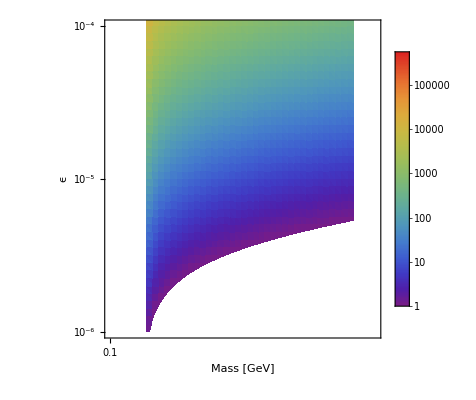

production_estimate.png

```mathematica
(* plot production *)
plotProduction = ListDensityPlot[production,ScalingFunctions->{"Log","Log","Log"},PlotRange->{{0.1,0.15},{0.000001,0.0001},{0.999,1000000}},PlotLegends->Automatic,ColorFunction->"Rainbow",FrameStyle->Gray,FrameLabel->{"Mass [GeV]","ϵ"}]
Export["production_estimate.png",plotProduction]
```

```mathematica
(* production and decay -> detectable events *)
detectable=Flatten[Table[{m,ϵ,Ndetectable[E0,m,ϵ]},{m,masses},{ϵ,epsilons}],1];
```

Less::nord: Invalid comparison with 0.-2.1632×10^7 ⅈ attempted.

Less::nord: Invalid comparison with 0.-2.14765×10^7 ⅈ attempted.

Less::nord: Invalid comparison with 0.-2.13216×10^7 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

Less::nord: Invalid comparison with 0.-9.1163×10^6 ⅈ attempted.

Less::nord: Invalid comparison with 0.-9.23197×10^6 ⅈ attempted.

Less::nord: Invalid comparison with 0.-9.34801×10^6 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

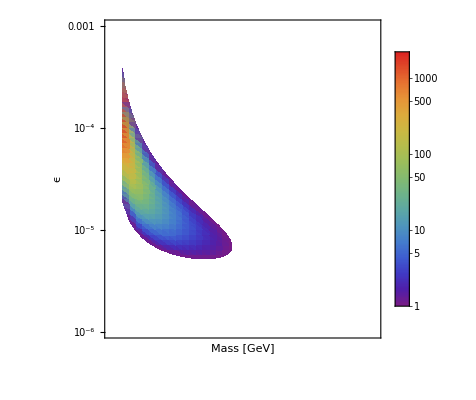

detectable_estimate.png

```mathematica
plotDetectable=ListDensityPlot[detectable,
ScalingFunctions->{"Log","Log","Log"},
PlotRange->{{0.105,0.15},{0.000001,0.001},{0.99,10000}},
PlotLegends->Automatic,
ColorFunction->"Rainbow",
FrameStyle->Gray,
InterpolationOrder->1,
FrameLabel->{"Mass [GeV]","ϵ"},
Mesh->Full
]
Export["detectable_estimate.png",plotDetectable]
```

```mathematica
(* decay length in lab frame *)
steps=35;
masseslog=Range[Log10[0.1058],Log10[0.2],(Log10[0.2]-Log10[0.1058])/steps];
masses=10^masseslog
epsilonslog=Range[-6,-3.2,0.05];
epsilons=10^epsilonslog
Tuples[{epsilons,masses}];

decaylengths=Flatten[Table[{m,ϵ,E0/m*c*τDLS[m,ϵ]},{m,masses},{ϵ,epsilons}],1];
```

{0.1058,0.107742,0.109721,0.111735,0.113786,0.115876,0.118003,0.12017,0.122376,0.124623,0.126911,0.129241,0.131614,0.13403,0.136491,0.138997,0.141549,0.144148,0.146794,0.149489,0.152234,0.155029,0.157875,0.160774,0.163725,0.166731,0.169793,0.17291,0.176085,0.179317,0.18261,0.185962,0.189377,0.192853,0.196394,0.2}

{1.×10^-6,1.12202×10^-6,1.25893×10^-6,1.41254×10^-6,1.58489×10^-6,1.77828×10^-6,1.99526×10^-6,2.23872×10^-6,2.51189×10^-6,2.81838×10^-6,3.16228×10^-6,3.54813×10^-6,3.98107×10^-6,4.46684×10^-6,5.01187×10^-6,5.62341×10^-6,6.30957×10^-6,7.07946×10^-6,7.94328×10^-6,8.91251×10^-6,0.00001,0.0000112202,0.0000125893,0.0000141254,0.0000158489,0.0000177828,0.0000199526,0.0000223872,0.0000251189,0.0000281838,0.0000316228,0.0000354813,0.0000398107,0.0000446684,0.0000501187,0.0000562341,0.0000630957,0.0000707946,0.0000794328,0.0000891251,0.0001,0.000112202,0.000125893,0.000141254,0.000158489,0.000177828,0.000199526,0.000223872,0.000251189,0.000281838,0.000316228,0.000354813,0.000398107,0.000446684,0.000501187,0.000562341,0.000630957}

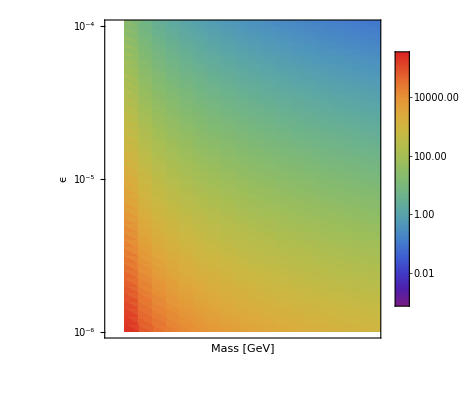

decay_lengths.png

```mathematica
plotDecay=ListDensityPlot[decaylengths,
ScalingFunctions->{"Log","Log","Log"},
PlotRange->{{0.10566,0.15},{0.000001,0.0001},{0.0001,10000000}},
PlotLegends->Automatic,
ColorFunction->"Rainbow",
FrameStyle->Gray,
InterpolationOrder->1,
FrameLabel->{"Mass [GeV]","ϵ"},
Mesh->Full
]
Export["decay_lengths.png",plotDecay]
```